# Beam PixeLink Last Updated: 03/06/2022

```mathematica
Quit[];
```

## File Location & Name

```mathematica
(*set directory and filetype*)
SetDirectory["/Users/claytonho/Documents/Research/Mathematica/Beams/Data"];
imgName="397_raw.bmp";
```

## Prep

## Plotting Setup

```mathematica
SetOptions[Plot,ImageSize->Large,PlotRange->Full];
SetOptions[ListPlot,ImageSize->Large,PlotRange->Full];
```

```mathematica
Off[General::munfl];
```

## Global Variables

```mathematica
inch=2.54*^-2;
cm=1*^-2;mm=1*^-3;um=1*^-6;nm=1*^-9;
```

```mathematica
pixelWidth=4.4*^-6;(*length per pixel for pixelink camera*)
```

## Image Import

```mathematica
imdRaw=ImageData[ColorConvert[Import[imgName],"Grayscale"]];
imgDim=Dimensions[imdRaw]//Reverse;
```

## Process Image

```mathematica
(*gaussian kernel, i.e. 2σ*)
nGauss=30;
(*range of pixels to take in*)
window={500,500};
```

## Gaussian Filter

```mathematica
imdGauss=GaussianFilter[imdRaw,nGauss];
center=Reverse[Position[imdGauss,Max[imdGauss]][[1]]];
```

## Center Image

```mathematica
{{x1,x2},{y1,y2}}=Transpose[Clip[{#-window[[1]],#+window[[1]]},{1,imgDim[[1]]}]]&/@center;
```

```mathematica
imdProcessed=imdRaw[[y1;;y2,x1;;x2]];
```

Part::take: Cannot take positions 206 through 1206 in {{0.00392157,0.00784314,0.00784314,0.,0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00784314,«1590»},{0.00784314,0.0117647,0.00784314,0.0117647,0.0117647,0.00392157,0.00784314,0.0117647,0.00784314,0.00784314,«1590»},«7»,{0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00392157,0.0117647,0.00392157,0.00392157,0.0117647,«1590»},«1190»}.

## Fit Image

## Fit Setup

```mathematica
{xVals,yVals}={Total[#],Total[#//Transpose]}&[imdProcessed];
```

```mathematica
(*fitting constraints; note - adding constraints may hurt fitting*)
xFitConstr={};
yFitConstr={};
```

```mathematica
(*factor of 2 in exponent is b/c intensity is square of electric field*)
xFitEqn={a(Exp[-2((x-x0)/wx)^2])+b};
yFitEqn={a(Exp[-2((y-y0)/wy)^2])+b};
```

```mathematica
(*fitting parameters*)
xFitVars={{x0,Min[{center[[1]],500}]},{wx,300},{a,Max[xVals]},{b,Min[xVals]}};
yFitVars={{y0,Min[{500,center[[2]]}]},{wy,150},{a,Max[yVals]},{b,Min[yVals]}};
```

## Fitting

```mathematica
(*fit!*)
xFit=NonlinearModelFit[xVals,Join[xFitEqn,xFitConstr],xFitVars,x,MaxIterations->1*^6];
yFit=NonlinearModelFit[yVals,Join[yFitEqn,yFitConstr],yFitVars,y,MaxIterations->1*^6];
```

NonlinearModelFit::srect: Value Total[{{0.00392157,0.00784314,0.00784314,0.,0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00784314,«1590»},{0.00784314,0.0117647,0.00784314,0.0117647,0.0117647,0.00392157,0.00784314,0.0117647,0.00784314,0.00784314,«1590»},«7»,{0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00392157,0.0117647,0.00392157,0.00392157,0.0117647,«1590»},«1190»}⟦206;;1206,396;;1396⟧] in search specification {a,Total[{{0.00392157,0.00784314,0.00784314,0.,0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00784314,«1590»},{0.00784314,0.0117647,0.00784314,0.0117647,0.0117647,0.00392157,0.00784314,0.0117647,0.00784314,0.00784314,«1590»},«7»,{0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00392157,0.0117647,0.00392157,0.00392157,0.0117647,«1590»},«1190»}⟦206;;1206,396;;1396⟧]} is not a number or array of numbers.

NonlinearModelFit::srect: Value Total[Transpose[{{0.00392157,0.00784314,0.00784314,0.,0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00784314,«1590»},{0.00784314,0.0117647,0.00784314,0.0117647,0.0117647,0.00392157,0.00784314,0.0117647,0.00784314,0.00784314,«1590»},«7»,{0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00392157,0.0117647,0.00392157,0.00392157,0.0117647,«1590»},«1190»}⟦206;;1206,396;;1396⟧]] in search specification {a,Total[Transpose[{{0.00392157,0.00784314,0.00784314,0.,0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00784314,«1590»},{0.00784314,0.0117647,0.00784314,0.0117647,0.0117647,0.00392157,0.00784314,0.0117647,0.00784314,0.00784314,«1590»},«7»,{0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00392157,0.0117647,0.00392157,0.00392157,0.0117647,«1590»},«1190»}⟦206;;1206,396;;1396⟧]]} is not a number or array of numbers.

```mathematica
{xFitParams,yFitParams}={xFit["ParameterTable"],yFit["ParameterTable"]}
```

NonlinearModelFit::srect: Value Total[{{0.00392157,0.00784314,0.00784314,0.,0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00784314,«1590»},{0.00784314,0.0117647,0.00784314,0.0117647,0.0117647,0.00392157,0.00784314,0.0117647,0.00784314,0.00784314,«1590»},«7»,{0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00392157,0.0117647,0.00392157,0.00392157,0.0117647,«1590»},«1190»}⟦206;;1206,396;;1396⟧] in search specification {a,Total[{{0.00392157,0.00784314,0.00784314,0.,0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00784314,«1590»},{0.00784314,0.0117647,0.00784314,0.0117647,0.0117647,0.00392157,0.00784314,0.0117647,0.00784314,0.00784314,«1590»},«7»,{0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00392157,0.0117647,0.00392157,0.00392157,0.0117647,«1590»},«1190»}⟦206;;1206,396;;1396⟧]} is not a number or array of numbers.

NonlinearModelFit::srect: Value Total[Transpose[{{0.00392157,0.00784314,0.00784314,0.,0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00784314,«1590»},{0.00784314,0.0117647,0.00784314,0.0117647,0.0117647,0.00392157,0.00784314,0.0117647,0.00784314,0.00784314,«1590»},«7»,{0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00392157,0.0117647,0.00392157,0.00392157,0.0117647,«1590»},«1190»}⟦206;;1206,396;;1396⟧]] in search specification {a,Total[Transpose[{{0.00392157,0.00784314,0.00784314,0.,0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00784314,«1590»},{0.00784314,0.0117647,0.00784314,0.0117647,0.0117647,0.00392157,0.00784314,0.0117647,0.00784314,0.00784314,«1590»},«7»,{0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00392157,0.0117647,0.00392157,0.00392157,0.0117647,«1590»},«1190»}⟦206;;1206,396;;1396⟧]]} is not a number or array of numbers.

NonlinearModelFit::srect: Value Total[{{0.00392157,0.00784314,0.00784314,0.,0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00784314,«1590»},{0.00784314,0.0117647,0.00784314,0.0117647,0.0117647,0.00392157,0.00784314,0.0117647,0.00784314,0.00784314,«1590»},«7»,{0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00392157,0.0117647,0.00392157,0.00392157,0.0117647,«1590»},«1190»}⟦206;;1206,396;;1396⟧] in search specification {a,Total[{{0.00392157,0.00784314,0.00784314,0.,0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00784314,«1590»},{0.00784314,0.0117647,0.00784314,0.0117647,0.0117647,0.00392157,0.00784314,0.0117647,0.00784314,0.00784314,«1590»},«7»,{0.00784314,0.00784314,0.00784314,0.00784314,0.0117647,0.00392157,0.0117647,0.00392157,0.00392157,0.0117647,«1590»},«1190»}⟦206;;1206,396;;1396⟧]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

$Aborted[]

## Extract Values

```mathematica
{wxFit,wyFit}=pixelWidth*{xFitParams[[1,1,3,2]],yFitParams[[1,1,3,2]]};
{wxFitErr,wyFitErr}=pixelWidth*{xFitParams[[1,1,3,3]],yFitParams[[1,1,3,3]]};
```

## Show

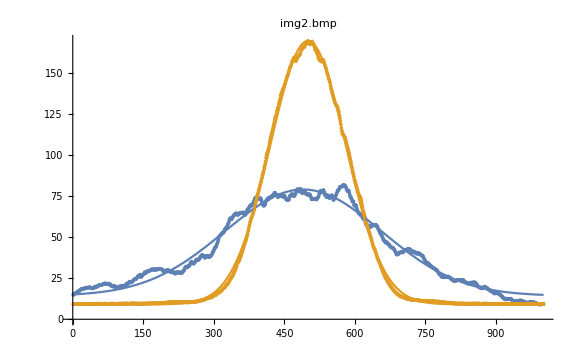
{(w_x=1466.35±11.4μm
w_y=704.071±1.μm),-Graphics-}

```mathematica
{
MatrixForm[{"w_x="<>ToString[wxFit/um//N]<>"±"<>ToString[Round[wxFitErr/um//N,0.1]]<>"μm","w_y="<>ToString[wyFit/um//N]<>"±"<>ToString[Round[wyFitErr/um//N,0.1]]<>"μm"}],
(*ListPlot[Max/@imdRaw,ImageSize->Large,PlotRange->{0,1},PlotLabel->"Clipping Check"],*)
Show[{
ListPlot[{xVals,yVals},ImageSize->Medium],
Plot[{xFit[x],yFit[x]},{x,0,2 *window[[1]]+1}]
},ImageSize->Large,PlotLabel->imgName]
}
```